```mathematica
Table[Rectangle[{i, 1},{i + 2, 1}], {i, -1, 6}]
```

{Rectangle[{-1,1},{1,1}],Rectangle[{0,1},{2,1}],Rectangle[{1,1},{3,1}],Rectangle[{2,1},{4,1}],Rectangle[{3,1},{5,1}],Rectangle[{4,1},{6,1}],Rectangle[{5,1},{7,1}],Rectangle[{6,1},{8,1}]}

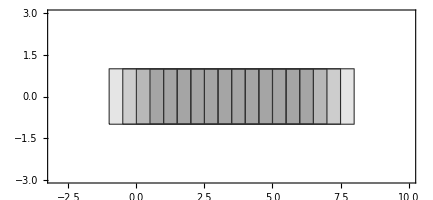

```mathematica
Graphics[{EdgeForm[GrayLevel[.2]],FaceForm[Opacity[.1]],Table[Rectangle[{i, -1},{i + 2, 1}], {i, -1, 6, .5}]}, PlotRange->{{-3, 10}, {-3, 3}}, Frame->True]
```

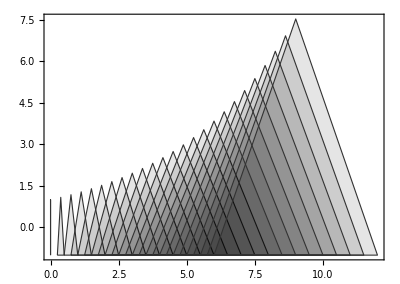

```mathematica
Graphics[{EdgeForm[GrayLevel[.2]],FaceForm[Opacity[.1]],Table[Triangle[{{i, -1},{1.5i, 1.4^i}, {2i, -1}}], {i,0, 6, .25}]},  Frame->True]
```

```mathematica
Graphics[{EdgeForm[GrayLevel[.2]],FaceForm[Opacity[.1]],Table[Triangle[{{i, -1},{i + 1, 1}, {i + 2, -1}}], {i, -1, 6, .5}]}, PlotRange->{{-3, 10}, {-3, 3}}, Frame->True]
```

```mathematica
data=NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{0,0},"Velocity"->{0,.5}|>,<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,-.5}|>,<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>},4]
```

NBodySimulationData[3, <4.>]

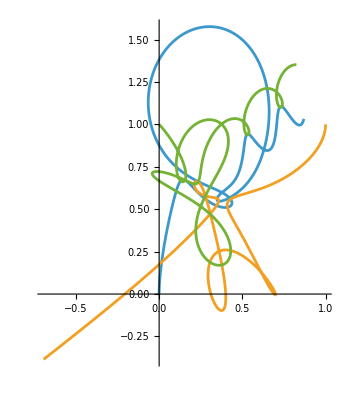

```mathematica
ParametricPlot[Evaluate[data[All,"Position",t]],{t,0,4}]
```

```mathematica
data[All,"Position",2]
```

{{0.304798,1.57616},{0.297257,0.0619309},{0.397945,0.361908}}